{{x→InterpolatingFunction[{{0., 0.9}}, <>],y→InterpolatingFunction[{{0., 0.9}}, <>],ψ→InterpolatingFunction[{{0., 0.9}}, <>]}}

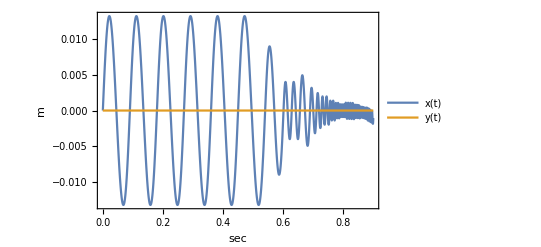

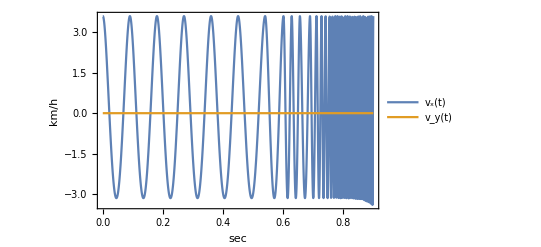

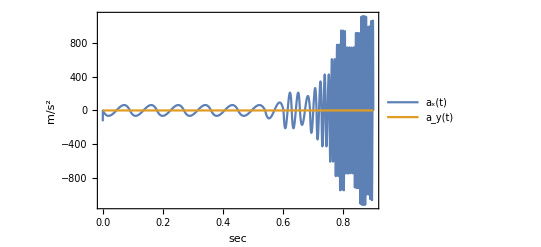

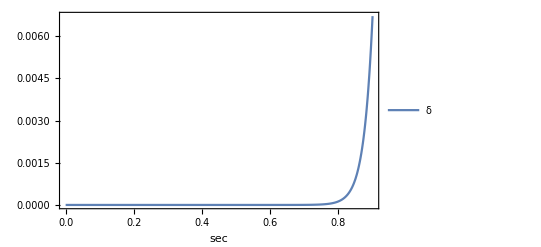

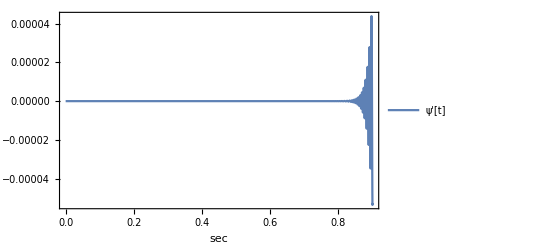

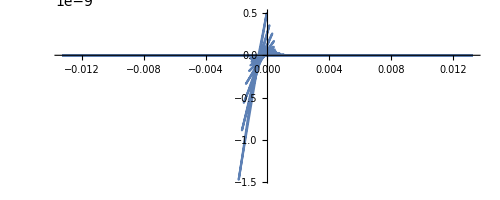

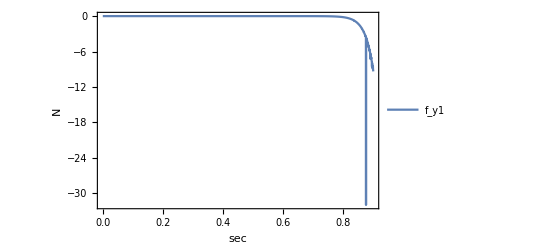

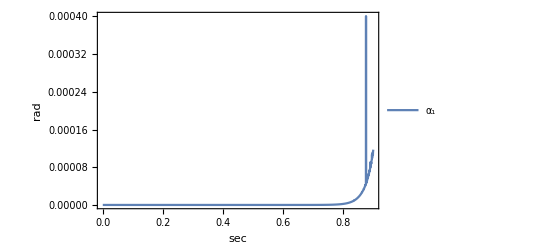

```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)]);
Brake[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
S1[t_,τ1_,δ1_]:=δ1/2*(Tanh[20t]-Tanh[20(t-τ1)]);
S2[t_,τ01_,τ1_,δ1_]:=Fold[Plus,0,Table[S1[t-τ01⟦k⟧,τ1⟦k⟧,δ1⟦k⟧],{k,1,Length[τ1]}]];
Subscript[β, r] = Brake[t,τ0 ,τ ,β];
η = √(1.0-Subscript[β, r]^2);
δ = S2[t,τ01,τ1,δ1];

Slip angle;
f[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f[Subscript[μ, 1],Subscript[F, z1],Subscript[C, α1]]; Subscript[α, sl2]=f[Subscript[μ, 2],Subscript[F, z2],Subscript[C, α2]];
Subscript[α, sl3]=f[Subscript[μ, 3],Subscript[F, z3],Subscript[C, α3]]; Subscript[α, sl4]=f[Subscript[μ, 4],Subscript[F, z4],Subscript[C, α4]];

f[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
Subscript[α, 1]=f[δ,Subscript[l, f]]; Subscript[α, 2]=f[δ,Subscript[l, f]];
Subscript[α, 3]=f[0,Subscript[l, r]]; Subscript[α, 4]=f[0,Subscript[l, r]];

Tire  Lateral Force;
f[C_,α_,μ_,F_,αs_]:=Piecewise[{{ - C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3,Abs[α]<αs},{-η μ F Sign[α],Abs[α]≥αs}}]/.rules;
Subscript[f, y1]=f[Subscript[C, α1],Subscript[α, 1],Subscript[μ, 1],Subscript[F, z1],Subscript[α, sl1]]/.rules; Subscript[f, y2]=f[Subscript[C, α2],Subscript[α, 2],Subscript[μ, 2],Subscript[F, z2],Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f[Subscript[C, α3],Subscript[α, 3],Subscript[μ, 3],Subscript[F, z3],Subscript[α, sl3]]/.rules; Subscript[f, y4]=f[Subscript[C, α4],Subscript[α, 4],Subscript[μ, 4],Subscript[F, z4],Subscript[α, sl4]]/.rules;

Tire  Longitudinal Force;
f[μ_,F_]:=Subscript[β, r] μ F/.rules;
Subscript[f, x1]=f[Subscript[μ, 1],Subscript[F, z1]]/.rules; Subscript[f, x2]=f[Subscript[μ, 2],Subscript[F, z2]]/.rules;
Subscript[f, x3]=f[Subscript[μ, 3],Subscript[F, z3]]/.rules; Subscript[f, x4]=f[Subscript[μ, 4],Subscript[F, z4]]/.rules;

Long. and Lat. Tot. Forces;
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];

Equations of Motion;
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules;
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules;
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4])/.rules;

rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->0,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

time =0.9;

τ0 = {0,10,20,50};
τ = {0.6,5,5,5};
β={0.00,0,-0.5,0.6};

τ01 = {0,1,10,102,135 ,140};
τ1 = {0.2,0.01,0.1,4,3 ,20};
δ1={0.00,-0.02,0,0,-0.025,0.025};

initCond={x[0]==0.00,x'[0]==1,y[0]==0.00,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0.00};
solution=NDSolve[{Eq1,Eq2,Eq3,initCond},{x,y,ψ},{t,0,time}]

f[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;

f[x[t],y[t],m,x[t],"y(t)"]
f[x'[t]*3.6,y'[t]*3.6,"km/h","v_x(t)","v_y(t)"]
f[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"]
f[-δ*180/π,,"","δ",""]
f[ψ'[t]*180/π,,"","ψ'[t]",""]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},PlotRange-> All]
f[Subscript[f, y1],,"N","f_y1",""]
f[Subscript[α, 1],,"rad","α_1",""]
```

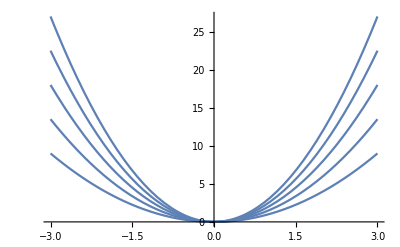

```mathematica
g[x_,y_,γ_]:=γ x^2+y
Plot3D[Table[g[x,γ],{γ,1,3,.5}],{x,-3,3},Plot]
```

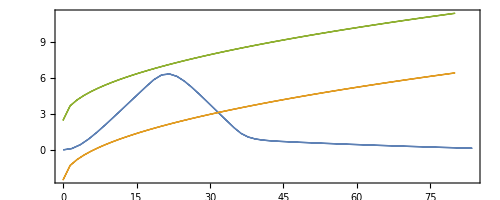

```mathematica
ParametricPlot[{{x[t],y[t]}/.solution,{z,z^(1/2)-2.5},{z,z^(1/2)+2.5}},{z,0,80},{t,0,time},PlotRange-> All]
```